# LIFLibrary

## Written by Maurizio Mattia, 2018

Library of functions computing eigenvalues and eigenfunctions of the Fokker-Plank operator L for the leaky-IF (LIF) neuron. Formulas are from (Brunel & Hakim, Neural Comput 1999) and (Deniz & Rotter, Phys Rev E 2017). 
Special thanks to Gianni Valerio Vinci for helpful discussions, pointing out an error in the normalization factor of eigenfunctions Φ_n expressed as a combination of parabolic cylinder functions and contributing to understand bifurcation of DD λs

## Numerical expression for the gain function Φ of LIF neurons

To conclude we can put together all these results to compose a fast and precise numerical implementation of the gain function Φ for the LIF neuron.

```mathematica
Psi[w_]=If[w≥-3,ⅇ^(w^2)(Erf[w]+1),2/(√π)NIntegrate[ⅇ^(-y^2)ⅇ^(2y w),{y,0,5}]];
```

#### For large |a| and |b|:

```mathematica
MFPT1[a_,b_]:=√π NIntegrate[Psi[w],{w,a,b}];
```

#### For relatively small |a| and |b|:

```mathematica
MFPTfrom0[b_]=√π DawsonF[b]Psi[b]-2∫_0^b DawsonF[x]ⅆx;
MFPTto0[a_]=-MFPTfrom0[a];
MFPT2[a_,b_]=MFPTfrom0[b]+MFPTto0[a];
```

#### For large b≫10:

At very strong subthreshold regime we expect to have huge mean FPTs. Setting as upper limit for the mean FPT of 10^100 times the decay constant τV, the upper bound is b<15. After this safely can be assumed MFTP[a,b]→∞.

```mathematica
FindRoot[Log[MFPTfrom0[b]]==100Log[10],{b,1}][[1]]
```

b→15.2449

#### For a≤b≤0:

```mathematica
MFPT3[a_,b_]:=NIntegrate[((ⅇ^(2 b w)-ⅇ^(2 a w))/w)Exp[-w^2],{w,0,∞}]
```

### Here is the optimal estimate of mean FPT in unit of τV

```mathematica
MFPT[a_,b_]:=If[b≤0,MFPT3[a,b],If[b>15,∞,If [a≤0,MFPT3[a,0]+MFPT2[0,b],MFPT2[a,b]]]]
```

```mathematica
Phi[μ_,σ_,τ_,H_,θ_,Tarp_]:=1/(Tarp+τ MFPT[(H-μ)/σ,(θ-μ)/σ]);
```

Here is the resulting plot to be compared to the one produced with the first approximated expression for Φ (see at the beginning of the notebook).

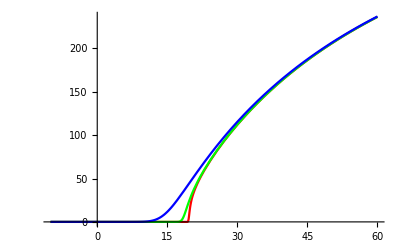

```mathematica
Plot[{Phi[μ,0.25,0.010,10,20,0.002],Phi[μ,1,0.010,10,20,0.002],Phi[μ,4,0.010,10,20,0.002]},{μ,-10,60},PlotStyle->{Red,Green,Blue},PlotRange->All]
```

### Other useful functions to fix μ and σ

Given the firing rate ν and the mean input current μ, which is the value of σ?

```mathematica
GetSigma[ν_,μ_,τ_,Vr_,Vt_,Tarp_]:=σ/.FindRoot[Phi[μ,σ,τ,Vr,Vt,Tarp]==ν,{σ,10.0}];
```

In the limit σ→0 what is the maximum value of μ at fixed ν?

```mathematica
V[t]/.Last[DSolve[{τ V'[t]==-V[t]+μ τ,V[0]==Vr},V[t],t]]
```

ⅇ^(-t/τ) (Vr-μ τ+ⅇ^(t/τ) μ τ)

```mathematica
Solve[%==Vt,t]
```

{{t→ConditionalExpression[τ (2 ⅈ π C[1]+Log[(-Vr+μ τ)/(-Vt+μ τ)]),C[1]∈ℤ]}}

```mathematica
Solve[τ Log[(-Vr+μ τ)/(-Vt+μ τ)]+Tarp==1/ν,μ]
```

{{μ→ConditionalExpression[(-Vr+ⅇ^((1-Tarp ν)/(ν τ)) Vt)/((-1+ⅇ^((1-Tarp ν)/(ν τ))) τ),-π<Im[(1-Tarp ν)/(ν τ)]≤π]}}

```mathematica
MaxMu[ν_,τ_,Vr_,Vt_,Tarp_]:=(-Vr+ⅇ^((1-Tarp ν)/(ν τ)) Vt)/((-1+ⅇ^((1-Tarp ν)/(ν τ))) τ);
```

## Implementing (Denis & Rotter, 2017) formulas (and few alternatives)

Independent solutions of the following Sturm-Liouville problem [Eqs. (A2) and (A3)]:

```mathematica
ϕ1DR[x_,λ_]:=Hypergeometric1F1[1/2-λ/2,1/2,-x^2];
```

```mathematica
ϕ2DR[x_,λ_]:=Gamma[λ/2]/Gamma[(λ+1)/2] Hypergeometric1F1[(1-λ)/2,1/2,-x^2]+2x Hypergeometric1F1[1-λ/2,3/2,-x^2];
```

Characteristic equation (CE) whose solution gives the eigenvalues of the Fokker-Planck (FP) operator [Eq. (A8)]:

```mathematica
CE[λ_,Xr_,Xt_]:= ϕ2DR[Xt,λ] ⅇ^(Xt^2)-  ϕ2DR[Xr,λ] ⅇ^(Xr^2);
```

This version of the CE is rather robust to find the real eigenvalues of the FP at strong drift-dominated regime:

```mathematica
CEDD[λ_,Xr_,Xt_]:= ⅇ^λ((ⅇ^(-Xr^2))/Gamma[λ/2] ϕ2DR[Xt,λ]-(ⅇ^(-Xt^2))/Gamma[λ/2] ϕ2DR[Xr,λ]);
```

Another independent solution resulting from Mathematica and the its related CE (not used in the following):

```mathematica
ϕ2DRH[x_,λ_]:=-ⅇ^(-x^2) HermiteH[-λ,x];
```

```mathematica
CEH[λ_,Xr_,Xt_]:= ϕ2DRH[Xt,λ] ⅇ^(Xt^2)-  ϕ2DRH[Xr,λ] ⅇ^(Xr^2);
```

Coefficients a[λ], b[λ] and d[λ] from Eqs. (A9) and (A10) to compose the eigenfunctions of the FP operator:

```mathematica
aDR[λ_,Xr_]:=ⅇ^(Xr^2)ϕ2DR[Xr,λ];
```

note that due to the characteristic equation aDR[λ,Xr] == aDR[λ,Xt].

```mathematica
bDR[λ_,Xt_]:=-ⅇ^(Xt^2)ϕ1DR[Xt,λ];
```

```mathematica
dDR[λ_,Xr_,Xt_]:=ⅇ^(Xr^2)ϕ1DR[Xr,λ]-ⅇ^(Xt^2)ϕ1DR[Xt,λ];
```

Here are the eigenfunctions ϕ[λ] for any λ ≠ 0:

```mathematica
ϕDR[x_,λ_,Xr_,Xt_]:=If[x≥Xr,aDR[λ,Xr]ϕ1DR[x,λ]+bDR[λ,Xt]ϕ2DR[x,λ],dDR[λ,Xr,Xt]ϕ2DR[x,λ]];
```

```mathematica
DerϕDR[x_,λ_,Xr_,Xt_]=-1/2(aDR[λ,Xr]D[ϕ1DR[x,λ], x]+bDR[λ,Xt]D[ϕ2DR[x,λ], x]);
flux[μτ_,στ_,λτ_]:=Module[{Xr,Xt},
Xr=(Vr-μτ)/στ; Xt=(Vt-μτ)/στ;DerϕDR[Xt,λτ,Xr,Xt]];
```

while these are the eigenfunctions ψ[λ] of the adjoint FP operator (B10):

```mathematica
ψDRNN[x_,λ_]:=ⅇ^(x^2)ϕ2DR[x,λ]; (* This is the not normalized version. *)
RelXmin=5; (* This set the lower bound of the integral to compute the inner products. *)
ψDR[x_,λ_,Xr_,Xt_]:=ψDRNN[x,λ]/NIntegrate[ψDRNN[y,λ]ϕDR[y,λ,Xr,Xt],{y,Xr-RelXmin(Xt- Xr),Xt}];
```

Here is the stationary probability density, the eigenfunction associated to λ=0. It is an elaboration of Eq. (3.10) in (Brunel & Hakim, 1999):

```mathematica
ϕBH0[x_,Xr_,Xt_]:=(√π)/MFPT[Xr,Xt] ⅇ^(-x^2)(Erfi[Xt]-If[x≤Xr,Erfi[Xr],Erfi[x]])
```

```mathematica
flux0[μτ_,στ_]:=Module[{Xr,Xt},
Xr=(Vr-μτ)/στ; Xt=(Vt-μτ)/στ;1/MFPT[Xr,Xt]];
```

### Formulas based on parabolic cylinder function D_ν(z)

```mathematica
ϕ1DRD[x_,λ_]:=2^(λ/2-1)/(√π)Gamma[(λ+1)/2] ⅇ^(-x^2/2)(ParabolicCylinderD[-λ,√2 x]+ParabolicCylinderD[-λ,-√2 x]);
ϕ2DRD[x_,λ_]:=2^(λ/2)/(√π)Gamma[λ/2] ⅇ^(-x^2/2)ParabolicCylinderD[-λ,-√2 x];
```

```mathematica
CEDorig[λ_,Xr_,Xt_]:= ϕ2DRD[Xt,λ] ⅇ^(Xt^2)-  ϕ2DRD[Xr,λ] ⅇ^(Xr^2);
```

```mathematica
CED[λ_,Xr_,Xt_]:= 1/Sin[(π λ)/2](-λ/ⅇ)^(λ/2)(ⅇ^(Xt^2/2) ParabolicCylinderD[-λ,-√2 Xt]-ⅇ^(Xr^2/2)ParabolicCylinderD[-λ,-√2 Xr]);
```

```mathematica
aDRD[λ_,Xr_]:=ⅇ^(Xr^2)ϕ2DRD[Xr,λ];
bDRD[λ_,Xt_]:=-ⅇ^(Xt^2)ϕ1DRD[Xt,λ];
dDRD[λ_,Xr_,Xt_]:=ⅇ^(Xr^2)ϕ1DRD[Xr,λ]-ⅇ^(Xt^2)ϕ1DRD[Xt,λ];
```

```mathematica
ϕDRD[x_,λ_,Xr_,Xt_]:=If[x≥Xr,aDRD[λ,Xr]ϕ1DRD[x,λ]+bDRD[λ,Xt]ϕ2DRD[x,λ],dDRD[λ,Xr,Xt]ϕ2DRD[x,λ]];
```

```mathematica
DerϕDRD[x_,λ_,Xr_,Xt_]=-1/2(aDRD[λ,Xr]D[ϕ1DRD[x,λ], x]+bDRD[λ,Xt]D[ϕ2DRD[x,λ], x]);
```

```mathematica
ψDRDNN[x_,λ_]:=ⅇ^(x^2)ϕ2DRD[x,λ]; (* This is the not normalized version. *)
RelXmin=5; (* This set the lower bound of the integral to compute the inner products. *)
ψDRD[x_,λ_,Xr_,Xt_]:=ψDRDNN[x,λ]/NIntegrate[ψDRDNN[y,λ]ϕDRD[y,λ,Xr,Xt],{y,Xr-RelXmin(Xt- Xr),Xt}];
```

## Compute eigenvalues λ

### Given a guess for the λs returns their exact values

```mathematica
GetLambdasFromGuess[Xr_,Xt_,λτ0_]:=
Module[{λτ,λτ1,ndx,NumericalZero=10^-10},
If[Depth[λτ0]==1,λτ1={λτ0},λτ1=λτ0];
λτ=Table[
If[Im[λτ1[[n]]]==0,
If[Xt==-Xr,
λτ/.FindRoot[CE[λτ,Xr,Xt]==0,{λτ,Re[λτ1[[n]]]}],
λτ/.FindRoot[CEDD[λτ,Xr,Xt]==0,{λτ,Re[λτ1[[n]]]}]
],
λτ/.FindRoot[CED[λτ,Xr,Xt]==0,{λτ,λτ1[[n]]}]
],
{n,Length[λτ1]}];

ndx=Flatten[Position[λτ,x_/;Re[x]>0]];
If[Length[ndx]>0,Print["Warning: ", Length[ndx]," eigenvalues result to have Re[λ]>0."]];

ndx=Flatten[Position[Table[
Min[Abs[CE[λτ[[n]],Xr,Xt]],Abs[CED[λτ[[n]],Xr,Xt]],Abs[CEDD[λτ[[n]],Xr,Xt]]],
{n,Length[λτ]}],x_/;x>NumericalZero]];
If[Length[ndx]>0,Print["Warning: ", Length[ndx]," eigenvalues do not satisfy CE[λ]==0 ",ndx,"."]];

(* λτ=SortBy[λτ,-Re[#]&] *)
If[Length[λτ]==1,λτ=λτ[[1]]];
λτ
]
```

### Return the DD λs at bifurcation, i.e. Xr == -Xt

```mathematica
GetDDLambdasAtBifurcation[Xt_,NumOfLambdas_]:=
Module[{λτ0},
(* The theoretical guesses. *)
λτ0=Table[(-3 n^2 π^2+3 Xt^2-Xt^4)/(6 Xt^2),{n,NumOfLambdas}];
(* Refines numerically the above guesses. *)
GetLambdasFromGuess[-Xt,Xt,λτ0] 
];
```

### Guess for real DD λs (OBSOLETE)

Previous guess is correct only under the assumption of μ τ much greater than Vt. If this is not the case we keep only the real part and for the imaginary part we take the following expression:

```mathematica
α[k_,Xr_,Xt_]:=((2π k)/(Xt-Xr))^2;
β[Xr_,Xt_]:=((Xt+Xr)/2)^2;
γ[k_,Xr_,Xt_]:=(-4 k^2 π^2+2 Xr (Xr-Xt) Log[1+√(1-ⅇ^(-2 Xr (Xr-Xt)))]+Log[1+√(1-ⅇ^(-2 Xr (Xr-Xt)))]^2)/(2(Xr-Xt)^2);
LambdaDDGuess[k_,Xr_,Xt_]:=If[Xt==-Xr,1/2-(k^2 π^2)/(2 Xt^2)-Xt^2/6,If[k>1,γ[k,Xr,Xt]+ⅈ √(α[k,Xr,Xt] β[Xr,Xt]),2γ[k,Xr,Xt]+ⅈ √(α[k,Xr,Xt] β[Xr,Xt])]];
LambdaDD[k_,Xr_,Xt_]:=λ/.FindRoot[CED[λ,Xr,Xt]==0,{λ,LambdaDDGuess[k,Xr,Xt]}];
```